```mathematica
Integrate[ 1+x^2 (-5/2+(3 Abs[x])/2),{x,-1,1}]
```

13/12

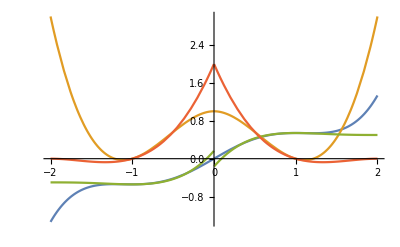

```mathematica
Plot[{Sign[x] *(Abs[x]-(5 Abs[x]^3)/6+(3 x^4)/8),1+x^2 (-5/2+(3 Abs[x])/2),Sign[x]*(2 Abs[x]-2 x^2+(5 Abs[x]^3)/6-x^4/8-1/6),(((5/2)-(1/2)*Abs[x])*Abs[x]-4)*Abs[x]+2},{x,-2,2}]
```

```mathematica
Integrate[(((5/2)-(1/2)*x)*x-4)*x+2,x]
```

2 x-2 x^2+(5 x^3)/6-x^4/8

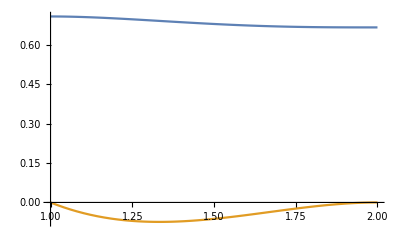

```mathematica
Plot[{2 x-2 x^2+(5 x^3)/6-x^4/8,(((5/2)-(1/2)*x)*x-4)*x+2},{x,1.,2.}]
```

```mathematica
f[x_]:=((3/2)*x-(5/2))*x^2+1
```

```mathematica
Integrate[f[x],x]
```

x-(5 x^3)/6+(3 x^4)/8

```mathematica
h[x_] := x-(5 x^3)/6+(3 x^4)/8
```

```mathematica
h[1]
```

13/24

```mathematica
h2[x_]:=2 x-2 x^2+(5 x^3)/6-x^4/8
```

```mathematica
h2[1] - h[1]
```

1/6